## 6 - ring Hubbard model

6 - Hubbard model ring

#### Basis for the sector with Sz sector (s1,s2)

```mathematica
n = 6;
E0 = 10;
s1 = 3;
s2 = 3;
base =.;
j = 0;
For[i = 0, i < 4^n, i++, vec = IntegerDigits[i, 2, 2 n];
n1 = Total[Take[vec, {1, n}]];
n2 = Total[Take[vec, {n + 1, 2 n}]];
If [n2 == s2 && n1 == s1, 
j++;
base[j] = vec]];
size = j;
```

#### Basis size

```mathematica
size
base[2]
```

90

{0,0,0,0,0,1,0,0,0,1,0,1}

#### Some diagonal operators: double occupancy in site i, Sz in site i, ...

```mathematica
up[x_] := Take[x, {1, n}];
dn[x_] := Take[x, {n + 1, 2 n}];
nn[x_] := Total[up[x] * dn[x]];
norm[x_] := Total[Abs[x]];
diag[i_]:=Table[base[k][[i]] * base[k][[i + n]], {k, 1, size}]
Double[i_] := DiagonalMatrix[
Table[base[k][[i]] * base[k][[i + n]], {k, 1, size}]
];
DoubleSiteAvg := Total[Table[Double[i], {i, 1, n}]] /n;
OpSz[i_] := DiagonalMatrix[Table[base[k][[i]] - base[k][[i + n]], {k, 1, size}]];
OpSzSz[i_, j_] := OpSz[i].OpSz[j];

nn[base[2]];
diag[2];
DoubleSiteAvg;
```

#### Hopping matrix

```mathematica
hop = Join[Table[i + j, {i, 1, n - 1}, {j, 0, 1}],
	Table[i - j, {i, 2, n}, {j, 0, 1}], {{n, 1}, {1, n}},
	Table[i + j, {i, n + 1, 2 n - 1}, {j, 0, 1}],
	Table[i - j, {i, n + 2, 2 n}, {j, 0, 1}], {{2 n, n + 1}, {n + 1, 2 n}}];
Length[hop];
hop;
```

#### Hopping Hamiltonian in many-body basis

```mathematica
HopTest[x_, y_, cre_, anh_] :=
norm[x - y] == 2&&
x[[cre]] == 1 &&
x[[anh]] == 0 &&
y[[cre]] == 0 &&
y[[anh]] == 1;
HopSign[x_, anh_] := (-1)^Total[Take[x, {anh + 1, 2 n}]];
H1 = Table[0, {i, 1, size}, {j, 1, size}];

For[i = 1, i ≤ Length[hop], i++, 
cre = hop[[i]][[1]];
anh = hop[[i]][[2]];
	For[bra = 1, bra ≤ size, bra++,
		For[ket = 1, ket ≤ size, ket++, 
If[HopTest[base[bra], base[ket], cre, anh],H1[[bra]][[ket]] +=HopSign[base[bra], cre] * HopSign[base[ket], anh]
]
]
]
];
H1//MatrixForm;
```

#### Other non-diagonal operators Local interaction (sum over all sites):

```mathematica
H2 = DiagonalMatrix[Table[nn[base[i]], {i, 1, size}]];
Shift = DiagonalMatrix[Table[E0 * (s1 + s2) , {i, 1, size}]];
H2;
```

#### Hubbard Hamiltonian as a function of local interaction U

```mathematica
H[u_] := N[H1 + u * H2 + Shift];
Egs[u_] := Eigenvalues[H[u], -1][[1]];
gs[u_] := Eigenvectors[H[u], -1][[1]];
Hpom[t_] := N[t * H1 + 10 * H2 + Shift];
```

#### Eigen-energies as a function of U

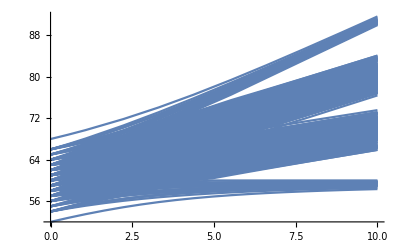

```mathematica
Plot[Sort[Eigenvalues[H[u]]],{u,0,10},PlotPoints->10,MaxRecursion->1]
```

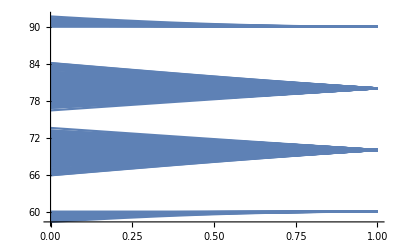

```mathematica
Plot[Sort[Eigenvalues[Hpom[1-t]]],{t,0,1},PlotPoints->10,MaxRecursion->1]
```

#### Ground state expectation value of operator A

```mathematica
Expect0[A_,u_]:=gs[u].A.gs[u];
```

#### Average double occupancy

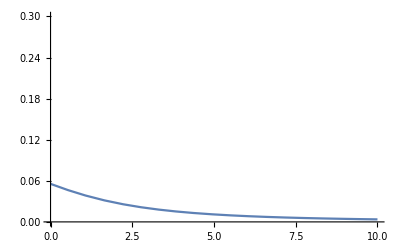

```mathematica
Plot[Expect0[DoubleSiteAvg,u],{u,0,10},PlotPoints->10,MaxRecursion->1,PlotRange->{0,0.3}]
```

#### Average ordered spin moment

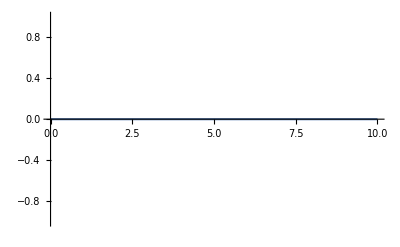

```mathematica
Plot[Expect0[OpSz[1],u],{u,0,10},PlotPoints->10,MaxRecursion->1,PlotRange->{-1,1}]
```

#### Average amplitude of the spin moment Sz^2

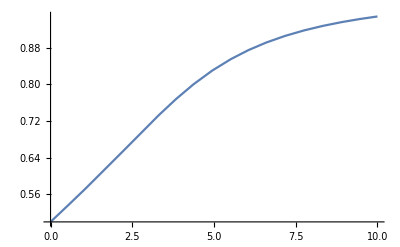

```mathematica
Plot[Expect0[OpSzSz[1,1],u]-Expect0[OpSz[1],u]^2,{u,0,10},PlotPoints->10,MaxRecursion->1]
```

#### Spin spin correlation function (instantaneous) <Sz(i)Sz(j)>

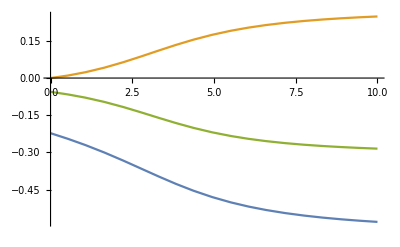

```mathematica
Plot[{Expect0[OpSzSz[1,2],u],Expect0[OpSzSz[1,3],u],Expect0[OpSzSz[1,4],u]},{u,0,10},PlotPoints->10,MaxRecursion->1]
```

```mathematica
Local susceptibility
```

Local susceptibility

```mathematica
Localchi[i_,u_]:=Module[{vec,eig,gs,E0,chi=0},
vec=Eigenvectors[H[u]];
eig=Eigenvalues[H[u]];
gs=vec[[size]];
E0=eig[[size]];
For[k=1,k<size-1,k++;
chi=chi+(gs.OpSz[i].vec[[k]])^2/(eig[[k]]-E0)];
2*chi];
```

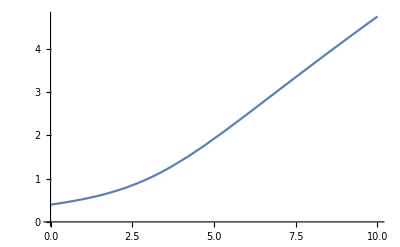

```mathematica
Plot[Localchi[1,u],{u,0,10},PlotPoints->20,MaxRecursion->1]
```

```mathematica
Staggered susceptibility
```

```mathematica
OpStaggered=Sum[(-1)^i*OpSz[i],{i,1,n}];
Staggeredchi[u_]:=Module[{vec,eig,gs,E0,chi=0},
vec=Eigenvectors[H[u]];
eig=Eigenvalues[H[u]];
gs=vec[[size]];E0=eig[[size]];
For[k=1,k<size-1,k++;
chi=chi+(gs.OpStaggered.vec[[k]])^2/(eig[[k]]-E0)];2*chi];
```

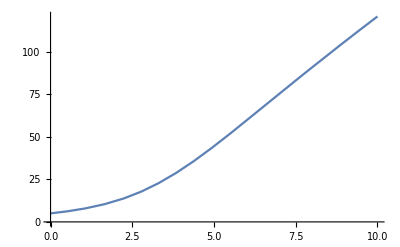

```mathematica
Plot[Staggeredchi[u],{u,0,10},PlotPoints->10,MaxRecursion->1]
```

#### Translation symmetry

```mathematica
klist=.;
klist=Table[Exp[I*2 π/n*k],{k,0,n-1}]
```

{1,ⅇ^((ⅈ π)/3),ⅇ^((2 ⅈ π)/3),-1,ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/3)}

#### Bloch sum

```mathematica
SzList=Table[OpSz[i],{i,1,n}];
Szk[k_]:=N[Sum[klist[[i]]^k*OpSz[i],{i,1,n}]];
SzkList=N[Table[Szk[k],{k,0,n}]];
SzSzk[k_,u_]:=Re[
		Expect0[SzkList[[k+1]].SzkList[[n-k+1]],u]
	];
```

```mathematica
Total[Total[Abs[Round[Szk[9],0.000001]]]]
```

552.

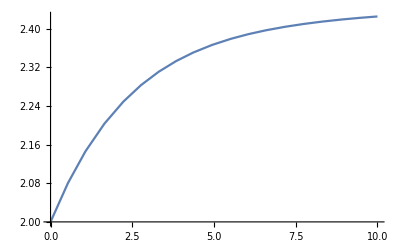

```mathematica
Plot[Re[Expect0[SzkList[[2]].SzkList[[6]],u]],{u,0,10},PlotPoints->10,MaxRecursion->1]
```

#### Correlation function in reciprocal space <Sz(k) Sz(-k)>

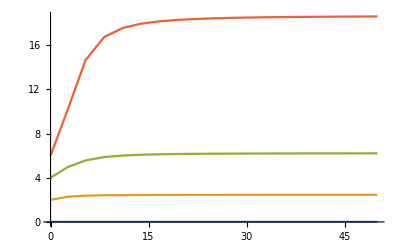

```mathematica
Plot[{SzSzk[0,u],SzSzk[1,u],SzSzk[2,u],SzSzk[3,u]},{u,0,50},PlotPoints->10,MaxRecursion->1]
```

```mathematica
Time dependent correlations
```

```mathematica
Matrix elements, Lorentzians, Re and Im susceptibility
```

```mathematica
Szzw[u_,i_,j_]:=Module[{vec,eig,gs,E0,chi},
vec=Eigenvectors[H[u]];
eig=Eigenvalues[H[u]];
gs=vec[[size]];(* Ground state is last entry, mathematica ordering*)
E0=eig[[size]]; (* Ground state is last entry*)
chi=0*eig;
For[k=1,k<size,k++;
	chi[[k]]=(gs.OpSz[i].vec[[k]])*(vec[[k]].OpSz[j].gs)
];
chi];

Szzkw[u_,i_,j_]:=Module[{vec,eig,gs,E0,chi},
vec=Eigenvectors[H[u]];
eig=Eigenvalues[H[u]];gs=vec[[size]];E0=eig[[size]];
chi=0*eig;
For[k=1,k<size,k++;
chi[[k]]=(gs.SzkList[[i]].vec[[k]])*(vec[[k]].SzkList[[j]].gs)
];
chi];

L[w_,x_,G_]:=G/(2 Pi)*1/((w-x)^2+G^2); 
RL[w_,x_,G_]:=(w-x)/((w-x)^2+G^2);

(*Calculate the Sum over all sandwiches, M is <n|Op|g>
Spect[w_,G_,M_,eig_]:=
	Module[{t=0},
		For[i=1,i≤Length[M],i++,
			If[Abs[M[[i]]]^2>0.000001,
				t=t+L[w,eig[[i]],G]*M[[i]]
			]
		];
t];

RSpect[w_,G_,M_,eig_]:=
	Module[{t=0},
		For[i=1,i≤Length[M]-1,i++;
			If[Abs[M[[i]]]^2>0.000001,
				t=t+RL[w,eig[[i]],G]*M[[i]]
			]
		];
-t];
eig=Eigenvalues[H[1]]-Eigenvalues[H[1]][[-1]];
```

#### Local spin - spin correlation function (spectrum = Im part)

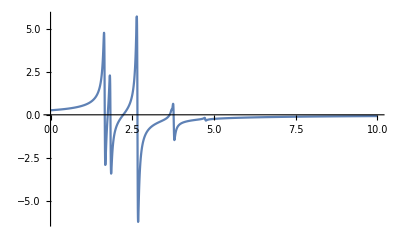

```mathematica
weigh=Szzw[1,1,1];
(*Table[{x,Spect[x,0.02,weigh,eig]},{x,0,10,0.005}];*)
Plot[RSpect[x,0.02,weigh,eig],{x,0,10},PlotRange->Full]
```

```mathematica
Round[weigh,0.0001];
```

#### k - dependent correlation function <S(k, w) S(-k, w)>

```mathematica
weigh1=Szzkw[1,2,6];
weigh2=Szzkw[1,3,5];
weigh3=Szzkw[1,4,4];
```

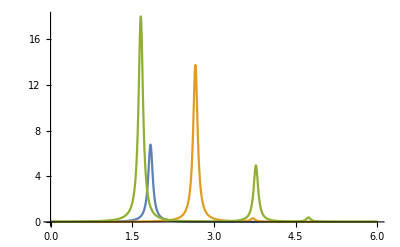

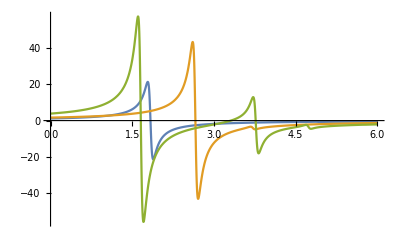

```mathematica
Plot[{
Spect[x,0.05,weigh1,eig],
Spect[x,0.05,weigh2,eig],
Spect[x,0.05,weigh3,eig]},
{x,0,6},PlotRange->Full]
Plot[{
RSpect[x,0.05,weigh1,eig],
RSpect[x,0.05,weigh2,eig],
RSpect[x,0.05,weigh3,eig]},
{x,0,6},PlotRange->Full]
```

```mathematica
Electronic propagators
```

#### construct subspaces with n + 1 and n - 1 particles

```mathematica
s1p=s1+1;
s1m=s1-1;
basep=.;
basem=.;
jp=0;
jm=0;
For[i=0,i<4^n,i++,
vec=IntegerDigits[i,2,2 n];
n1=Total[Take[vec,{1,n}]];
n2=Total[Take[vec,{n+1,2 n}]];
If[n2==s2&&n1==s1p,
jp++;
basep[jp]=vec;
];
If[n2==s2&&n1==s1m,
jm++;
basem[jm]=vec;
];
]
sizep=jp
sizem=jm
```

300

300

#### Construct the Hamiltonians in these subspaces

```mathematica
H2p=DiagonalMatrix[Table[nn[basep[i]],{i,1,sizep}]];
H2m=DiagonalMatrix[Table[nn[basem[i]],{i,1,sizem}]];
H1p=Table[0,{i,1,sizep},{j,1,sizep}];
For[i=1,i≤Length[hop],i++,
cre=hop[[i]][[1]];
anh=hop[[i]][[2]];
For[bra=1,bra≤sizep,bra++,
For[ket=1,ket≤sizep,ket++,
If[HopTest[basep[bra],basep[ket],cre,anh],
H1p[[bra]][[ket]]=HopSign[basep[bra],cre]*HopSign[basep[ket],anh]
]
]
]
];
H1m=Table[0,{i,1,sizem},{j,1,sizem}];
For[i=1,i≤Length[hop],i++,
cre=hop[[i]][[1]];
anh=hop[[i]][[2]];
For[bra=1,bra≤sizem,bra++,
For[ket=1,ket≤sizem,ket++,
If[HopTest[basem[bra],basem[ket],cre,anh],
H1m[[bra]][[ket]]+=HopSign[basem[bra],cre]*HopSign[basem[ket],anh]
]
]
]
];
```

#### calculated Eigen-energies and eigenvectors

```mathematica
Hp[u_]:=N[H1p+u*H2p+DiagonalMatrix[Table[E0 (s1+s2+1),{i,1,sizep}]]];
Ep[u_]:=Eigenvalues[Hp[u]];
Hm[u_]:=N[H1m+u*H2m+DiagonalMatrix[Table[E0 (s1+s2-1),{i,1,sizem}]]];
Em[u_]:=Eigenvalues[Hm[u]];
```

#### construct the creation n -> n + 1 and annihilation n -> n - 1 operators (on site and in k - space)

```mathematica
ctest[x_,y_,i_]:=
norm[x-y]==1&&
x[[i]]==0&&
y[[i]]==1;
OpC[site_]:=Module[{t=Table[0,{i,1,sizem},{j,1,size}]},
For[bra=1,bra≤sizem,bra++,
For[ket=1,ket≤size,ket++,
If[ctest[basem[bra],base[ket],site],
t[[bra]][[ket]]=HopSign[base[ket],site]
]
]
];
t]
OpCd[site_]:=Module[{t=Table[0,{i,1,sizep},{j,1,size}]},
For[bra=1,bra≤sizep,bra++,
For[ket=1,ket≤size,ket++,
If[ctest[base[ket],basep[bra],site],
t[[bra]][[ket]]=HopSign[basep[bra],site]
]
]
];
t]
Ck[k_]:=N[Sum[klist[[i]]^k*OpC[i],{i,1,n}]]/Sqrt[n];
Cdk[k_]:=N[Sum[klist[[i]]^(-k)*OpCd[i],{i,1,n}]/Sqrt[n]];
```

#### define the matrix elements | < n + 1 | a^+ | g > | ^2 and | < n - 1 | a | g > | ^2

```mathematica
Gpw[u_,i_,j_]:=Module[{vec,chi=ConstantArray[0,sizep],X=gs[u].Transpose[OpCd[i]],Y=OpCd[j].gs[u]},
vec=Eigenvectors[Hp[u]];
For[k=1,k<sizep,k++;
chi[[k]]=(X.vec[[k]])*(vec[[k]].Y)];
chi];
Gmw[u_,i_,j_]:=Module[{vec,chi=ConstantArray[0,sizem],X=gs[u].Transpose[OpC[i]],Y=OpC[j].gs[u]},vec=Eigenvectors[Hm[u]];
For[k=1,k<sizem,k++;
chi[[k]]=(X.vec[[k]])*(vec[[k]].Y)];
chi];
Gkpw[u_,j_]:=Module[{vec,chi=ConstantArray[0,sizep],Y=Cdk[j].gs[u]},
vec=Eigenvectors[Hp[u]];
For[k=1,k<sizep,k++;
chi[[k]]=(Abs[vec[[k]].Y])^2];
chi];
Gkmw[u_,j_]:=Module[{vec,chi=ConstantArray[0,sizem],Y=Ck[j].gs[u]},
vec=Eigenvectors[Hm[u]];
For[k=1,k<sizep,k++;
chi[[k]]=(Abs[vec[[k]].Y])^2];
chi];
```

#### precompute the matrix elements

```mathematica
U=1.;
weighp11=Gpw[U,1,1];
eigp=Eigenvalues[Hp[U]]-Egs[U];
weighm11=Gmw[U,1,1];
eigm=Eigenvalues[Hm[U]]-Egs[U];
mu=10+U/2;
weightkp0=Gkpw[U,0];
weightkm0=Gkmw[U,0];
weightkp1=Gkpw[U,1];
weightkm1=Gkmw[U,1];
weightkp2=Gkpw[U,2];
weightkm2=Gkmw[U,2];
weightkp3=Gkpw[U,3];
weightkm3=Gkmw[U,3];
plot4={
Plot[{Spect[x,0.05,weightkp0,eigp-mu],Spect[-x,0.05,weightkm0,eigm+mu]},{x,-7,7},PlotRange->Full],Plot[{Spect[x,0.05,weightkp1,eigp-mu],Spect[-x,0.05,weightkm1,eigm+mu]},{x,-7,7},PlotRange->Full],Plot[{Spect[x,0.05,weightkp2,eigp-mu],Spect[-x,0.05,weightkm2,eigm+mu]},{x,-7,7},PlotRange->Full],Plot[{Spect[x,0.05,weightkp3,eigp-mu],Spect[-x,0.05,weightkm3,eigm+mu]},{x,-7,7},PlotRange->Full],Plot[{Spect[x,0.05,weighp11,eigp-mu],Spect[-x,0.05,weighm11,eigm+mu]},{x,-7,7},PlotRange->Full]};
```

```mathematica
Plot Im G (w) for positive (electron addition) and negative (electron removal) frequencies for U = 1, 2, 3, 4
```

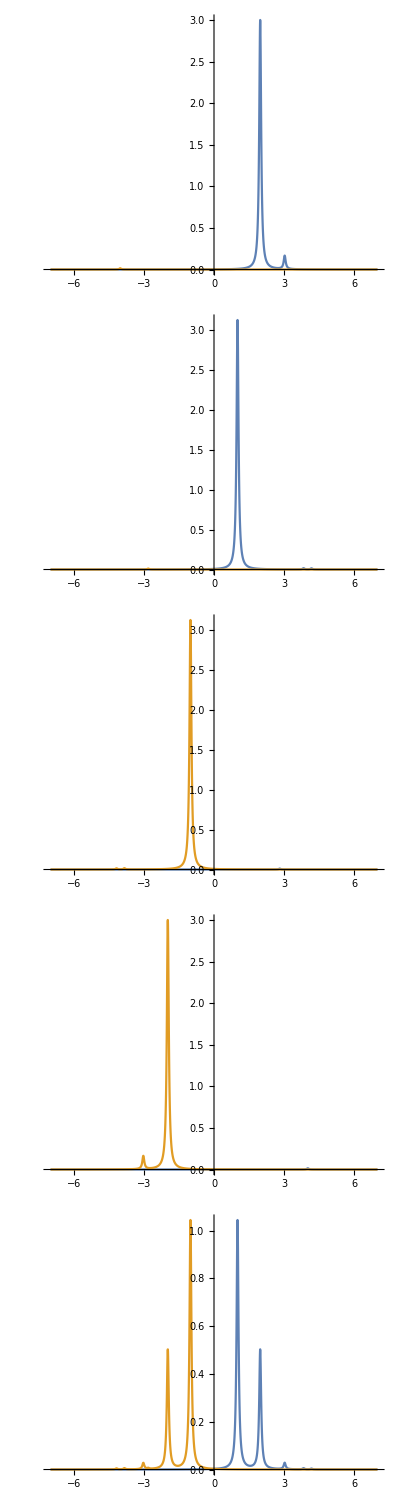
(-Graphics-)

```mathematica
{MatrixForm[plot1],MatrixForm[plot2],MatrixForm[plot3],MatrixForm[plot4]};
{plot1,plot2,plot3,plot4};
MatrixForm[plot4]
```

#### Finite field calculation of local susceptibility

```mathematica
field=0.01;
Htest=.;
gtest=.;
chitest=.;
Htest[u_,x_]:=H[u]-x*OpSz[1];
gtest[u_,x_]:=Eigenvectors[Htest[u,x]][[-1]];
chitest[u_,x_]:=gtest[u,x].OpSz[1].gtest[u,x]/x;
```

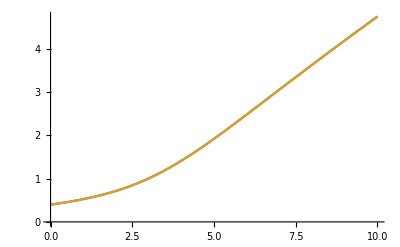

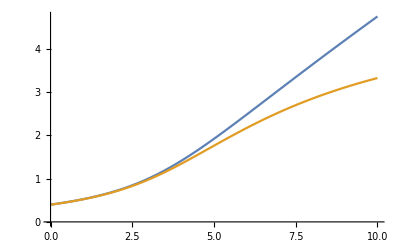

```mathematica
Plot[{Localchi[1,u],chitest[u,0.01]},{u,0,10}]
Plot[{Localchi[1,u],chitest[u,0.2]},{u,0,10}]
```